```mathematica
trikotnik={{3,0}, {5,4},{2,4}};
Stranice[{AA_, BB_, CC_}] := {
{BB, CC},
{CC, AA},
{AA, BB}
}
```

```mathematica
Koti[{AA_, BB_, CC_}] := {
{CC, AA, BB},
{AA, BB, CC},
{BB, CC, AA} }
```

```mathematica
Stranice[trikotnik]
```

{{{5,0},{7,4}},{{7,4},{0,0}},{{0,0},{5,0}}}

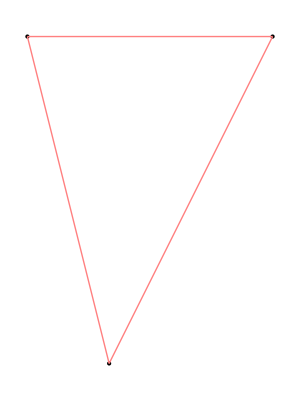

```mathematica
SlikaOglisc[trikotnik_] := Map[Point, trikotnik];
SlikaStranic[trikotnik_] :=Map[Line, Stranice[trikotnik]];
NarisiTrikotnik[trikotnik_] :=
Graphics[
{PointSize[Large], SlikaOglisc[trikotnik], {Pink, SlikaStranic[trikotnik]}}, AspectRatio->Automatic
]
NarisiTrikotnik[trikotnik]
```

```mathematica
VektorSimetraleKota[{x_,y_,z_}] := Normalize[Normalize[x-y]+Normalize[z-y]]
```

```mathematica
SimetralaKota[{x_,y_,z_}, dol_:10]:={y,y+VektorSimetraleKota[{x,y,z}]*dol}
```

```mathematica
SlikaSimetralKota[trikotnik_]:=Map[Line
```